# Linear Stability Analysis of Landslides

## Define perturbed variables and DAE

```mathematica
ClearAll["Global`*"]
ε=Symbol["ϵ"];
(*Define perturbed variables*)
H[x_,t_]:=H0[x]+ε h[x,t]
φ[x_,t_]:=1+ε ψ[x,t]
v[x_,t_]:=1+ε u[x,t]
(*Define the rule globally so you don't have to keep re-typing it*)H0Rule={D[H0[x],x]->-(f0 (1-λ)+4 b0 x-α+4 b0 x α^2+b0 α H0[x])};

(*Define the velocity expression*)
vDef=Exp[(1/A)*((α-4 b0 x (1+α^2)-D[H[x,t],x]-b0 α H[x,t])/(1-λ)-f0-B Log[φ[x,t]])];
(*Series expand with respect to epsilon*)
vLin=Series[vDef,{ε,0,1}]//Normal;
(*Substitute your steady state condition:H0'[x]+b0*alpha*H0[x]+...=0*)
uExpr=Simplify[vLin/.H0Rule]
uϵ=Coefficient[uExpr,ϵ]
```

(-A+A λ+b0 α ϵ h[x,t]-B ϵ (-1+λ) ψ[x,t]+ϵ h^(1,0)[x,t])/(A (-1+λ))

(b0 α h[x,t]-B (-1+λ) ψ[x,t]+h^(1,0)[x,t])/(A (-1+λ))

## Mass transport and Contact-state evolution equations

```mathematica
pdeH=D[H[x,t],t]+ζ D[H[x,t] v[x,t],x];
pdeφ=D[φ[x,t],t]+ζ v[x,t] D[φ[x,t],x]-(1-v[x,t] φ[x,t]);
(*pdeHlin=Series[pdeH/. v[x,t]->uExpr,{ε,0,1}]//Normal//ExpandAll;*)
(*pdeφlin=Series[pdeφ/. v[x,t]->uExpr,{ε,0,1}]//Normal//ExpandAll;*)
pdeHlin=(Series[pdeH,{ε,0,1}]//Normal//ExpandAll)/.{u[x,t]->uϵ,D[u[x,t],x]->D[uϵ,x]};
pdeφlin=(Series[pdeφ,{ε,0,1}]//Normal//ExpandAll)/.{u[x,t]->uϵ};
(*Extract Linear terms*)
pdeH1=Coefficient[pdeHlin,ε]/.H0Rule//FullSimplify
pdeφ1=Coefficient[pdeφlin,ε]/. H0Rule//FullSimplify
```

h^(0,1)[x,t]+ζ h^(1,0)[x,t]+(ζ (α-4 b0 x (1+α^2)+f0 (-1+λ)-b0 α H0[x]) (b0 α h[x,t]+(B-B λ) ψ[x,t]+h^(1,0)[x,t]))/(A (-1+λ))+(ζ H0[x] (b0 α h^(1,0)[x,t]+(B-B λ) ψ^(1,0)[x,t]+h^(2,0)[x,t]))/(A (-1+λ))

ψ[x,t]+ψ^(0,1)[x,t]+(b0 α h[x,t]+(B-B λ) ψ[x,t]+h^(1,0)[x,t])/(A (-1+λ))+ζ ψ^(1,0)[x,t]

## Local Stability Analysis using Fourier Modes

```mathematica
fourierRules={
h[x,t]->hHat,
ψ[x,t]->ψHat,
D[h[x,t],t]-> ω hHat,
D[ψ[x,t],t]-> ω ψHat,
D[h[x,t],x]->I k hHat,
D[h[x,t],x,x]->-k^2 hHat,
D[ψ[x,t],x]->I k ψHat};
(*Apply Fourier rules and assume x=0 for constant H0 case*)eq1=pdeH1/. fourierRules/. {x->x0,H0[x]->Subscript[H0, c]};
eq2=pdeφ1/. fourierRules/. {x->x0,H0[x]->Subscript[H0, c]};
(*Create the system of equations*)
system={eq1==0,eq2==0};
(*Extract the coefficient matrix for {hHat,ψHat}*)
Normal@CoefficientArrays[system,{hHat,ψHat}][[1]]
matrix=Normal@CoefficientArrays[system,{hHat,ψHat}][[2]];
(*Solve for the Dispersion Relation ω*)
dispersionRelation=Solve[Det[matrix]==0,ω]//FullSimplify;
Series[Simplify[Series[ω/.dispersionRelation,{ζ,0,1}]//Normal,Assumptions->{A-B>0,B>0}],{k,0,1}]
```

{0,0}

{(-1+B/A-(B b0 α ζ (f0+4 b0 x0-α+4 b0 x0 α^2-f0 λ+b0 α H0_c))/(A (A-B) (-1+λ)))-(ⅈ ζ (A^2 (-1+λ)-A B (-1+λ)+B (f0-α+4 b0 x0 (1+α^2)-f0 λ)) k)/(A (A-B) (-1+λ))+O[k]^2,(b0 α ζ (f0+4 b0 x0-α+4 b0 x0 α^2-f0 λ+b0 α H0_c))/((A-B) (-1+λ))-(ⅈ ζ (B+α-4 b0 x0 (1+α^2)+A (-1+λ)+f0 (-1+λ)-B λ) k)/((A-B) (-1+λ))+O[k]^2}

```mathematica
(*Evaluate the matrix at k=0*)
matrixK0=matrix/. {k->0}//FullSimplify;
(*Solve for the eigenvalues at k=0*)
longWaveω= Solve[Det[matrixK0]==0,ω]//FullSimplify
ω0=FullSimplify[longWaveω/.{ζ->0},Assumptions->{A-B>0,A>0}];
(*Extract expressions using simplifications for b0,ζ and VS friction*)
ω1=Simplify[Series[ω/.longWaveω,{ζ,0,1}]//Normal,Assumptions->{A-B>0,A>0}]
```

{{ω→1/(2 A (-1+λ))(B (-1+λ)+b0 α ζ (f0-α+4 b0 x0 (1+α^2)-f0 λ)+b0^2 α^2 ζ H0_c-A (-1+λ) (1+√(1/(A^2 (-1+λ)^2)(-2 A (b0 α ζ (α-4 b0 x0 (1+α^2)+f0 (-1+λ))+B (-1+λ)) (-1+λ)+A^2 (-1+λ)^2+(B+b0 α ζ (α-4 b0 x0 (1+α^2)+f0 (-1+λ))-B λ)^2+b0^2 α^2 ζ H0_c (-2 (A+B)+2 b0 α (f0-α+4 b0 x0 (1+α^2)) ζ+2 (A+B-b0 f0 α ζ) λ+b0^2 α^2 ζ H0_c)))))},{ω→1/(2 A (-1+λ))(B (-1+λ)+b0 α ζ (f0-α+4 b0 x0 (1+α^2)-f0 λ)+b0^2 α^2 ζ H0_c+A (-1+λ) (-1+√(1/(A^2 (-1+λ)^2)(-2 A (b0 α ζ (α-4 b0 x0 (1+α^2)+f0 (-1+λ))+B (-1+λ)) (-1+λ)+A^2 (-1+λ)^2+(B+b0 α ζ (α-4 b0 x0 (1+α^2)+f0 (-1+λ))-B λ)^2+b0^2 α^2 ζ H0_c (-2 (A+B)+2 b0 α (f0-α+4 b0 x0 (1+α^2)) ζ+2 (A+B-b0 f0 α ζ) λ+b0^2 α^2 ζ H0_c)))))}}

{-((A-B)^2+(B b0 α ζ (f0+4 b0 x0-α+4 b0 x0 α^2-f0 λ+b0 α H0_c))/(-1+λ))/(A (A-B)),(b0 α ζ (f0+4 b0 x0-α+4 b0 x0 α^2-f0 λ+b0 α H0_c))/((A-B) (-1+λ))}

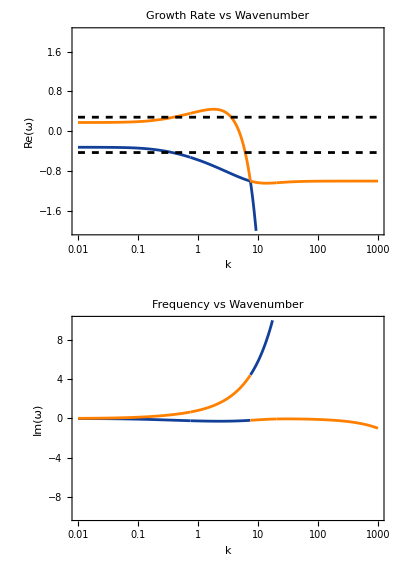

```mathematica
(*Example Plot:Change parameters for specific values*)
Aval=0.01;
Bval=0.008;
ζval=0.001;
λval=0.7;
f0val = 0.3;
b0val=0.1;
H0val = 0.1;
αval=1.0;
xval=-1;
ω01plot=ω1[[1]]/.{A->Aval,B->Bval,ζ->ζval,λ->λval,b0->b0val,f0->f0val,α->αval,x0->xval,Subscript[H0, c]->H0val};
ω02plot=ω1[[2]]/.{A->Aval,B->Bval,ζ->ζval,λ->λval,b0->b0val,f0->f0val,α->αval,x0->xval,Subscript[H0, c]->H0val};
(*Plot Re[ω] vs wave-number and analytic solutions at k=0*)
p1=LogLinearPlot[{Evaluate[Re[ω/. dispersionRelation/. {
A->Aval,B->Bval,
ζ->ζval,λ->λval,
Subscript[H0, c]->H0val,b0->b0val,
f0->f0val,α->αval,x0->xval}]],0*k+ω01plot,0*k+ω02plot},
{k,0.01,1000},
PlotStyle->{DarkBlue,Orange,{Black,Dashed},{Black,Dashed}},
PlotLabel->"Growth Rate vs Wavenumber",FrameLabel->{"k","Re(ω)"},
PlotRange->{-2,2},ImageSize->Medium,Frame->True,GridLines->Automatic];
p2=LogLinearPlot[Evaluate[Im[ω/. dispersionRelation/. {
A->Aval,B->Bval,
ζ->ζval,λ->λval,
Subscript[H0, c]->H0val,b0->b0val,
f0->f0val,α->αval,x0->xval}]],
{k,0.01,1000},
PlotStyle->{DarkBlue,Orange,{Black,Dashed},{Black,Dashed}},
PlotLabel->"Frequency vs Wavenumber",FrameLabel->{"k","Im(ω)"},
PlotRange->{-10,10},ImageSize->Medium,Frame->True,GridLines->Automatic];
GraphicsColumn[{p1,p2},Spacings->10]
```

```mathematica
ω2=Series[ω/.dispersionRelation[[2]],{ζ,0,2}]//Normal;
ω2real=Simplify[ComplexExpand[Re[ω2]],
Assumptions->{A-B>0,B>0,A>0,
1-λ>0,ζ>0,k>=0}]
kmax=Solve[D[ω2real,k]==0,k];
k/.kmax/.{
A->Aval,B->Bval,
ζ->ζval,λ->λval,
Subscript[H0, c]->H0val,b0->b0val,
f0->f0val,α->αval,x0->xval}
```

1/((A-B)^3 (-1+λ)^2)ζ ((f0-α+4 b0 x0 (1+α^2)-f0 λ) (A^2 b0 α (-1+λ)-2 A B b0 α (-1+λ)+B (B b0 α (-1+λ)+(k^2-b0^2 α^2) ζ (f0-α+4 b0 x0 (1+α^2)-f0 λ)))-(k^2+b0^2 α^2) (-A^2 (-1+λ)+2 A B (-1+λ)+B (B-B λ+2 b0 α ζ (f0-α+4 b0 x0 (1+α^2)-f0 λ))) H0_c-B (k^2+b0^2 α^2)^2 ζ H0_c^2)

{0,-12.1307,12.1307}

## Numerical Eigenvalue Problem

NDSolve::ndsz: At x == -0.938415, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 0.500313, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-3.27511×10^34] is too small to represent as a normalized machine number; precision may be lost.

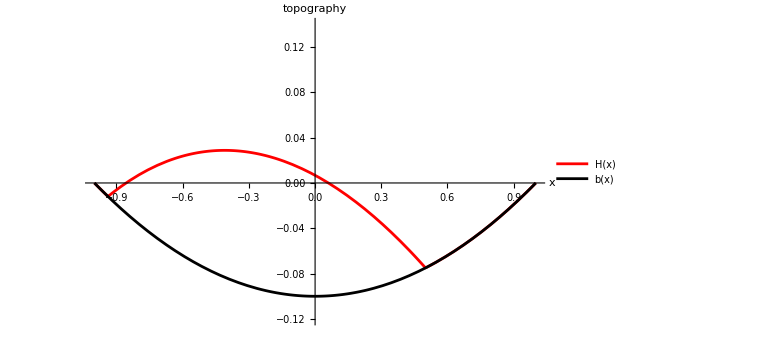

```mathematica
b=b0val*(x^2-1);(*basal geometry*)
xval=0.5;(*position of landslide toe*)
f0val0 = 0.6;λval0=0.0;
αval0=0.5;
eqnlogODE = -Exp[ϕ[x]]*D[ϕ[x],x] - 0.5*(α-D[b,x])/(1+(D[b,x])^2)*D[b,x,x]/(1+D[b,x]*α)*Exp[ϕ[x]] == f0+D[b,x] -(α-D[b,x])/(1+D[b,x]*α);
sollogss = NDSolve[{eqnlogODE/.{α->αval0,f0->f0val0*(1-λval0)},ϕ[xval]==Log[0.0001]},ϕ,{x,-1,1}];
H0num =  Exp[ϕ[x]/.sollogss];
Plot[{H0num+b,b},{x,-1,1},PlotStyle->{{Red},Black},AxesLabel->{"x","topography"},PlotLegends->{"H(x)","b(x)"},ImageSize->Large,PlotRange->{-1.2*b0val,1.4*b0val},LabelStyle->{FontSize->20}]
```

```mathematica
(*Define the operator expressions by isolating the time derivatives*)(*We replace Derivative[0,1][h][x,t] with ω h[x]*)
operatorRules={
h[x,t]->h[x],
ψ[x,t]->ψ[x],
D[h[x,t],t]->ω h[x],
D[ψ[x,t],t]->ω ψ[x],
D[h[x,t],x]->D[h[x],x],
D[h[x,t],{x,2}]->D[h[x],x,x],
D[ψ[x,t],x]->D[ψ[x],x]};
(*Apply rules to PDEs*)
eq1Spatial=pdeH1/. operatorRules
eq2Spatial=pdeφ1/. operatorRules;
(*Isolate the Omega terms to define the RHS for NDEigensystem*)solωH=Solve[eq1Spatial==0,ω][[1,1,2]]
solωψ=Solve[eq2Spatial==0,ω][[1,1,2]]
(*rhsH and rhsPsi will be functions of h[x],h'[x],h''[x],psi[x],psi'[x]*)
rhsH=solωH*h[x]/.H0[x]->H0num[x];
rhsψ=solωψ*ψ[x];
bcs={h[-1]==0,h[1]==0,
ψ[-1]==0};
(*Compute the first 6 global eigenvalues and eigenfunctions*)
{vals,funs}=NDEigensystem[{rhsH,rhsψ,bcs},{h,ψ},{x,-1,1},6];
```

ω h[x]+ζ h'[x]+(ζ (α-4 b0 x (1+α^2)+f0 (-1+λ)-b0 α H0[x]) (b0 α h[x]+(B-B λ) ψ[x]+h'[x]))/(A (-1+λ))+(ζ H0[x] (b0 α h'[x]+(B-B λ) ψ'[x]+h''[x]))/(A (-1+λ))

(-ζ h'[x]-(ζ (α-4 b0 x (1+α^2)+f0 (-1+λ)-b0 α H0[x]) (b0 α h[x]+(B-B λ) ψ[x]+h'[x]))/(A (-1+λ))-(ζ H0[x] (b0 α h'[x]+(B-B λ) ψ'[x]+h''[x]))/(A (-1+λ)))/h[x]

(-b0 α h[x]+A ψ[x]-B ψ[x]-A λ ψ[x]+B λ ψ[x]-h'[x]+A ζ ψ'[x]-A ζ λ ψ'[x])/(A (-1+λ) ψ[x])

NDEigensystem::numdep: The number of PDEs (5) does not match the number of dependent variables (2).

Set::shape: Lists {vals,funs} and NDEigensystem[{-ζ h'[x]-(ζ (α-4 b0 x (1+Power[«2»])+f0 (-1+λ)-b0 α {Power[«2»]}[x]) (b0 α h[x]+(B+Times[«3»]) ψ[x]+h'[x]))/(A (-1+λ))-(ζ {ⅇ^(InterpolatingFunction[{«1»},«3»,{«1»}][x])}[x] (b0 α h'[x]+(B+Times[«3»]) ψ'[x]+h''[x]))/(A (-1+λ)),(-b0 α h[x]+«11»)/(A (-1+λ)),{h[-1]==0,h[1]==0,ψ[-1]==0}},{h,ψ},{x,-1,1},6] are not the same shape.